```mathematica
UNET`$Verbose=True;
<<UNETDev`
```

## Generated Data

### Show 2D UNET

```mathematica
dim={112,112};
chan=2;
class=4;
feat=8;
```

```mathematica
MakeUNET[chan,class,feat,dim,BlockType->"UNet"]
```

```mathematica
MakeUNET[chan,class,feat,dim,BlockType->"UResNet"]
```

```mathematica
MakeUNET[chan,class,feat,dim,BlockType->"ResNet"]
```

```mathematica
MakeUNET[chan,class,feat,dim,BlockType->"UDenseNet"]
```

```mathematica
MakeUNET[chan,class,feat,dim,BlockType->"DenseNet"]
```

### Show 3D UNET

```mathematica
dim={32,64,64};
chan=2;
class=4;
feat=8;
```

```mathematica
MakeUNET[chan,class,feat,dim,BlockType->"UNET"]
```

```mathematica
MakeUNET[chan,class,feat,dim,BlockType->"UResNet"]
```

```mathematica
MakeUNET[chan,class,feat,dim,BlockType->"ResNet"]
```

```mathematica
MakeUNET[chan,class,feat,dim,BlockType->"UDenseNet"]
```

```mathematica
MakeUNET[chan,class,feat,dim,BlockType->"DenseNet"]
```

### Describe UNET

```mathematica
(*general*) 
nets={"Unet", "UResNet", "ResNet", "UDenseNet", "DenseNet"};
style={Bold,TextAlignment->Center,FontFamily->"Helvetica"};
lab=Style[#,style]&/@Join[{"features"},nets];
CountConv=Count[Head/@Information[#,"LayersList"],ConvolutionLayer]&;

(*parameters*)
dim3D={32,64,64};
dim2D=Drop[dim3D,1];
{nchan,nclass}={2,8};

dep={2,4,8,16,24,32};
par=Table[ToString[dep[[i]]],{i,1,Length[dep]}];
```

```mathematica
(*2D UNET generation*)
{par2D,mem2D}=Transpose@Table[
nets2D=MakeUNET[nchan,nclass, dep[[i]], dim2D, BlockType-># ]&/@nets;
{
Flatten@{par[[i]],Information[#,"ArraysTotalElementCount"]&/@nets2D},
Flatten@{par[[i]],Information[#,"ArraysTotalByteCount"]&/@nets2D}
}
,{i,1,Length[dep]}];
layers2D=ToString[CountConv[#]]&/@nets2D;
```

```mathematica
(*3D UNET generation*)
{par3D,mem3D}=Transpose@Table[
nets3D=MakeUNET[nchan,nclass, dep[[i]],dim3D,BlockType-># ]&/@nets;
{
Flatten@{par[[i]],Information[#,"ArraysTotalElementCount"]&/@nets3D},
Flatten@{par[[i]],Information[#,"ArraysTotalByteCount"]&/@nets3D}
}
,{i,1,Length[dep]}];
layers3D=ToString[CountConv[#]]&/@nets3D;
```

```mathematica
(*make Table*)
layers=Column[{Style["Number of convolution layers",style],Style["1)  UNet: "<>layers2D[[1]]<>"    2)  UResNet: "<>layers2D[[2]]<>
"    3)  ResNet: "<>layers2D[[3]]<>"    4)  UDenseNet: "<>layers2D[[4]]<>"    5)  DenseNet: "<>layers2D[[5]],style]},Alignment->Center];
tab1=Column[{Style["2D Nets - Numer of Array Elementes",style],
TableForm[par2D,TableHeadings->{None,lab},TableAlignments->Right]},Alignment->Center];
tab2=Column[{Style["3D Nets - Numer of Array Elementes",style],
TableForm[par3D,TableHeadings->{None,lab},TableAlignments->Right]},Alignment->Center];

Column[{layers,"",tab1,"",tab2},Alignment->Center]
```

```mathematica
(*make Table*)
layers=Column[{Style["Number of convolution layers",style],Style["1)  UNet: "<>layers2D[[1]]<>"    2)  UResNet: "<>layers2D[[2]]<>
"    3)  ResNet: "<>layers2D[[3]]<>"    4)  UDenseNet: "<>layers2D[[4]]<>"    5)  DenseNet: "<>layers2D[[5]],style]},Alignment->Center];
tab1=Column[{Style["2D Nets - Numer of Array bytes",style],
TableForm[mem2D,TableHeadings->{None,lab},TableAlignments->Right]},Alignment->Center];
tab2=Column[{Style["3D Nets - Numer of Array bytes",style],
TableForm[mem3D,TableHeadings->{None,lab},TableAlignments->Right]},Alignment->Center];

Column[{layers,"",tab1,"",tab2},Alignment->Center]
```

### Examples of Test Data

```mathematica
{data,label}=CreateImage1[];
Flatten@{MakeChannelImage[data],Image[label]}
```

```mathematica
{data,label}=CreateImage2[];
Flatten@{MakeChannelImage[data],MakeClassImage[label]}
```

```mathematica
{data,label}=CreateImage3[];
Flatten@{MakeChannelImage[data],MakeClassImage[label,{1,4}]}
```

```mathematica
{data,label}=CreateImage4[];
Flatten@{MakeChannelImage[data],MakeClassImage[label,{1,4}]}
```

### Test Cases 1: 1 channel - 1 classes

```mathematica
(*make test data*)
{data1,label1}=MakeTestImages[100,1];
```

```mathematica
(*split the data*)
{train1,valid1,testData1,testLabel1,order1}=SplitTrainData[data1,label1];
```

```mathematica
(*train the net*)
{{net1,trained1,netTrained1},{result1,iou1}}=TrainUNET[train1,valid1,{testData1,testLabel1},
TargetDevice->{"GPU",1},MaxTrainingRounds->250,NetParameters->2,DropoutRate->.5,BatchSize->32];
MakeNetPlots[trained1]
```

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData1,netTrained1]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData1,testLabel1,result1, NumberRowItems->3,MakeDifferenceImage->False]
```

```mathematica
(*visualize the test data with diff image*)
ShowChannelClassData[testData1,testLabel1,result1, NumberRowItems->3,MakeDifferenceImage->True]
```

### Test Case 2: 1 channel - 2 classes

```mathematica
(*make test data*)
{data2,label2}=MakeTestImages[100,2];
```

```mathematica
Dimensions@data2
Dimensions@label2
```

{100,1,128,128}

{100,128,128}

```mathematica
(*split the data*)
{train2,valid2,testData2,testLabel2,order}=SplitTrainData[data2,label2];
```

Dimensions data: {100,1,128,128} - Dimensions label: {100,128,128}

Number of Samples in each set: {70,20,10}

channels: 1 - classes: 2 - Dimensions :{128,128}

Evaluating test data

DICE per class: {1→0.971,2→0.859}

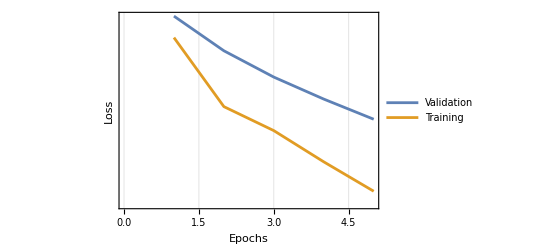
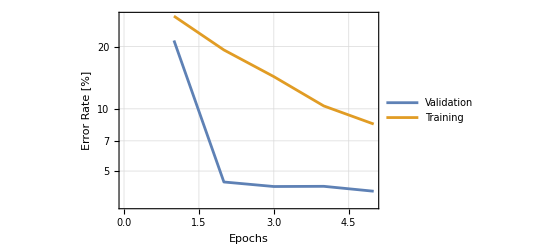

```mathematica
(*train the net*)
{{net2,trained2,netTrained2},{result2,iou2}}=TrainUNET[train2,valid2,{testData2,testLabel2},BatchSize->32,
TargetDevice->{"GPU",1},MaxTrainingRounds->250,NetParameters->2,
AugmentTrainData->{False,False,True}];
MakeNetPlots[trained2]
```

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData2,netTrained2]
```

```mathematica
Options[ShowChannelClassData]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData2, testLabel2,result2, NumberRowItems->3,MakeDifferenceImage->True,ClassStepSize->1]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

### Test Case 3: 1 channel - 4 classes

```mathematica
(*make test data*)
{data3,label3}=MakeTestImages[200,3];
```

```mathematica
(*split the data*)
{train3,valid3,testData3,testLabel3,order3}=SplitTrainData[data3,label3];
```

```mathematica
(*train the net*)
{{net3,trained3,netTrained3},{result3,iou3}}=TrainUNET[train3,valid3,{testData3,testLabel3},BatchSize->32,
TargetDevice->{"GPU",1},MaxTrainingRounds->500,NetParameters->32,
AugmentTrainData->{"90",False,True},BlockType->"ResNet"];
MakeNetPlots[trained3]
```

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData3,netTrained3]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData3, testLabel3, result3, NumberRowItems->3,
MakeDifferenceImage->True,ClassStepSize->1]
```

### Test Case 4 : 3 channels - 4 classes

```mathematica
(*make test data*)
{data4,label4}=MakeTestImages[100,4];
```

```mathematica
(*split the data*)
{train4,valid4,testData4,testLabel4,order4}=SplitTrainData[data4,label4];
```

```mathematica
(*train the net*)
{{net4,trained4,netTrained4},{result4,iou4}}=TrainUNET[train4,valid4,{testData4,testLabel4},
BatchSize->32,
TargetDevice->{"GPU",1},MaxTrainingRounds->200,NetParameters->16,
DropoutRate->0.5,AugmentTrainData->{"90",False,True}];
MakeNetPlots[trained4]
```

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData4,netTrained4]
```

```mathematica
(*visualize the test data with diff image*)
ShowChannelClassData[testData4, testLabel4,NumberRowItems->2,MakeDifferenceImage->True]
```

```mathematica
(*visualize the validation data with diff image*)
ShowChannelClassData[valid4[[;;9,1]],valid4[[;;9,2]],ClassDecoder[netTrained4[valid4[[1;;9,1]],TargetDevice->"GPU"],4],
 NumberRowItems->2,MakeDifferenceImage->True]
```

### Test Case 5 - same as 4 with animation

```mathematica
{data5,label5}=MakeTestImages[100,4];
```

```mathematica
{train5,valid5,testData5,testLabel5,order}=SplitTrainData[data5,label5];
```

```mathematica
(*choose a nice image*)
MakeChannelImage/@testData5
```

```mathematica
im=6;nchan=Max[testLabel5];solutions={};
imChan=First@MakeChannelImage[testData5[[im,{1}]]];
(*The monitoring function*)
monitor=AppendTo[solutions,ClassDecoder[NetExtract[#Net,"net"][testData5[[im]],TargetDevice->"GPU"],nchan]]&;
```

```mathematica
(*train the net with monitor function*)
{{net,trained,netTrained},{result,iou}}=TrainUNET[train5,valid5,{testData5,testLabel5},BatchSize->35,
 TargetDevice->{"GPU",1},MaxTrainingRounds->200,NetParameters->16,DropoutRate->.5,NetLossLayers->All,
AugmentTrainData->{"90",False,True},
TrainingProgressFunction->{monitor,"Interval"->Quantity[1,"Rounds"]}];
MakeNetPlots[trained]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData5, testLabel5, result, NumberRowItems->2,MakeDifferenceImage->True,ClassStepSize->1,ImageSize->650]
```

```mathematica
(*make the animation images*)
solIm=ColorReplace[MakeClassImage[#,{1,4}],ColorData["Rainbow"][0]]&/@solutions;
anim=Table[Show[ImageCompose[imChan,{sol,.5}],ImageSize->500],{sol,solIm}];

(*play the animatin*)
Animate[im,{im,anim}]
```

```mathematica
Export["anim-v2.gif",anim,"DisplayDuration"->.2,"AnimationRepetitions"->Infinity]
```